```mathematica
rho[x_]:= cte*x^2*1/((1+x^2)^3)
rho[x]
D[rho[x],x]
```

(cte x^2)/((1+x^2)^3)

-(6 cte x^3)/((1+x^2)^4)+(2 cte x)/((1+x^2)^3)

```mathematica
nb:=21969.3(* s*)
ni:= 2.96*10^(12)  (*s*)
xini = ni / nb
```

1.34733×10^8

```mathematica
c := 3*10^(10) 
g := 6.67*10^(-8)
ab:= 7.41155*10^(-9) (*sin dimensiones*)
cte =(3*c^2)/(8*π*g) *1/(ab^2*nb^2)
```

6.07502×10^34

```mathematica
rhoini := rho[xini]
rhoini
```

184.351

```mathematica
rhoNorm[x_]:= rho[x]/rhoini
```

```mathematica
Plot[rhoNorm[x],{x,-5,5}]
```

-Graphics-

```mathematica
Plot[rhoNorm[x],{x,-10^4,10^4}, Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
D[rhoNorm[x], x]
```

-(1.97721×10^33 x^3)/((1+x^2)^4)+(6.59071×10^32 x)/((1+x^2)^3)

```mathematica
Solve[D[rhoNorm[x], x]==0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.707107},{x→0.},{x→0.707107}}

```mathematica
rhoNorm[0.7071067811865476]
```

4.882×10^31

```mathematica
datosrho=Table[{x,rhoNorm[x]},{x,-5,5,0.01}];
Export["rhocf_sin_gasBH.csv",datosrho]
```

rhocf_sin_gasBH.csv

```mathematica
datosrho=Table[{x,rhoNorm[x]},{x,-10^4,10^4,0.01}];
Export["rhocf_sin_gasBH_largo.csv",datosrho]
```

rhocf_sin_gasBH_largo.csv

```mathematica
datosrho=Table[{x,rhoNorm[x]},{x,-10^(-8),10^(-8),10^(-12)}];
Export["rhocf_cerca_sin_gasBH.csv",datosrho]
```

rhocf_cerca_sin_gasBH.csv

```mathematica
FullSimplify[-(6 ctr x^3)/((1+x^2)^4)+(2 ctr x)/((1+x^2)^3)]
```

(ctr (2 x-4 x^3))/((1+x^2)^4)

```mathematica
Simplify[(ctr (2 x-4 x^3))/((1+x^2)^4)]
```

(ctr (2 x-4 x^3))/((1+x^2)^4)

```mathematica
drho[x_]:=(cte (2 x-4 x^3))/((1+x^2)^4)
omega[x_]:= (-(1+x^2))/(3*x)*1/rho[x]*drho[x] -1
```

```mathematica
omega[x]
```

-1-(0.333333 (2 x-4 x^3))/x^3

```mathematica
FullSimplify[-1-(2 x-4 x^3)/(3 x^3)]
```

1/3-2/(3 x^2)

```mathematica
omega[x_] := 1/3-2/(3 x^2)
```

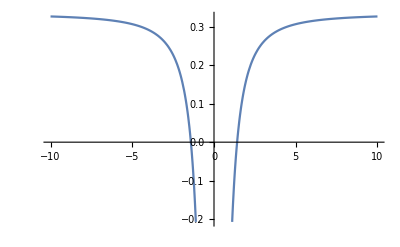

```mathematica
Plot[omega[x],{x,-10,10}]
```

```mathematica
pts=Subdivide[-10,10,100000]
tabla=Table[If[x==0, Nothing,{x,omega[x]}]{x,pts}]
Export["omega_sin_bh.csv",tabla]
```

omega_sin_bh.csv

```mathematica
datosomega=Table[If[x==0, Nothing,{x,omega[x]}],{x,-5,5,0.1}];
Export["omega_sin_gasBH.csv",datosomega]
```

omega_sin_gasBH.csv

```mathematica
datosomega=Table[If[x==0, Nothing,{x,omega[x]}],{x,-10^(-7),10^(-7),10^(-11)}];
Export["omega_cerca_sin_gasBH.csv",datosomega]
```

omega_cerca_sin_gasBH.csv

```mathematica
datosomega=Table[If[x==0, Nothing,{x,omega[x]}],{x,-10^8,10^8,1000}];
Export["omega_sin_gasBH_todo.csv",datosomega]
```

omega_sin_gasBH_todo.csv

```mathematica
Limit[omega[x], x->∞]
```

1/3